# Basic Operation Counts

## Matrix Multiplication

We want to make sure that

{64,128,256,512,1024,2048,4096,8192}

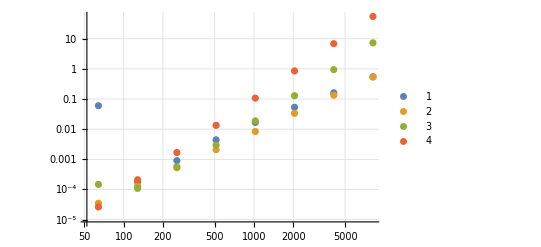

```mathematica
ms=2^Range[6,13]
Data=Table[
{
AbsoluteTiming[A=RandomReal[{-1,1},{m,m}];]⟦1⟧,
ByteCount[A],
AbsoluteTiming[A.A;]⟦1⟧
},
{m,ms}];
ListLogLogPlot[{
{ms,Data⟦All,1⟧}ᵀ,
{ms,Data⟦All,2⟧/10^9}ᵀ,
{ms,Data⟦All,3⟧}ᵀ,
{ms,10^(-10)*ms^3}ᵀ},
PlotLegends->Automatic,
GridLines->Automatic
]
```

## LU Decomposition

{64,128,256,512,1024,2048,4096,8192}

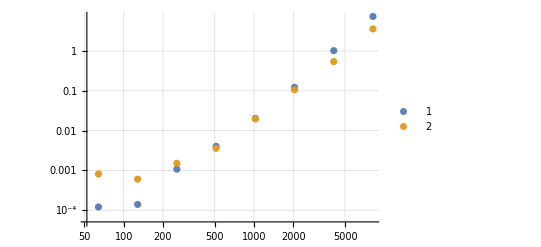

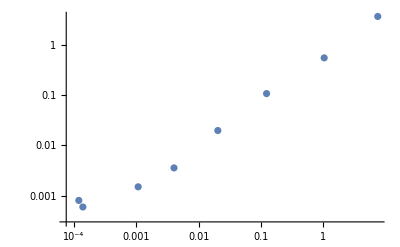

```mathematica
ms=2^Range[6,13]
Data=Table[
{
A=RandomReal[{-1,1},{m,m}];
AbsoluteTiming[A.A;]⟦1⟧,
AbsoluteTiming[LUDecomposition[A];]⟦1⟧
},
{m,ms}];
ListLogLogPlot[{
{ms,Data⟦All,1⟧}ᵀ,
{ms,Data⟦All,2⟧}ᵀ},
PlotLegends->Automatic,
GridLines->Automatic
]
ListLogLogPlot[Data]
```

## Eigen Decomposition

{64,128,256,512,1024,2048,4096,8192}

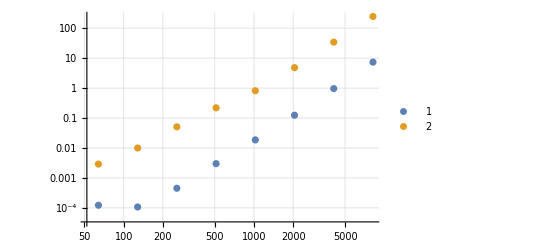

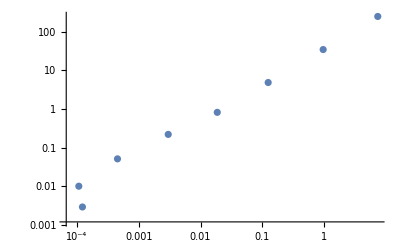

```mathematica
ms=2^Range[6,13]
Data=Table[
{
A=RandomReal[{-1,1},{m,m}];
AbsoluteTiming[A.A;]⟦1⟧,
AbsoluteTiming[Eigensystem[A];]⟦1⟧
},
{m,ms}];
ListLogLogPlot[{
{ms,Data⟦All,1⟧}ᵀ,
{ms,Data⟦All,2⟧}ᵀ},
PlotLegends->Automatic,
GridLines->Automatic
]
ListLogLogPlot[Data]
```

## Eigenvalues A=Aᵀ

{64,128,256,512,1024,2048,4096,8192}

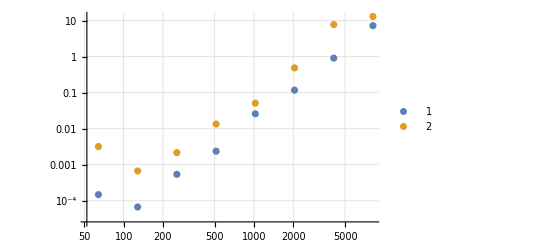

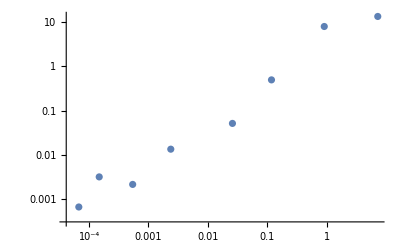

```mathematica
ms=2^Range[6,13]
Data=Table[
{
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
AbsoluteTiming[A.A;]⟦1⟧,
AbsoluteTiming[Eigenvalues[A];]⟦1⟧
},
{m,ms}];
ListLogLogPlot[{
{ms,Data⟦All,1⟧}ᵀ,
{ms,Data⟦All,2⟧}ᵀ},
PlotLegends->Automatic,
GridLines->Automatic
]
ListLogLogPlot[Data]
```